```mathematica
r[t_, a_,b_,n_]:=Sign[Cos[n(t+π/n)]](Abs[Cos[n(t+π/n)]])^a+b;
```

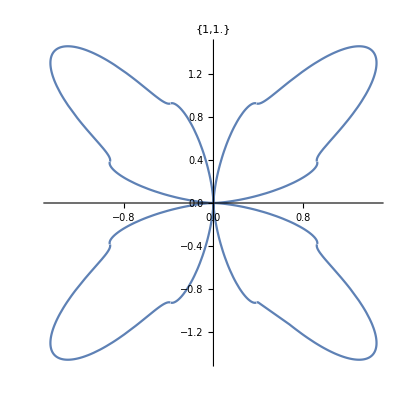
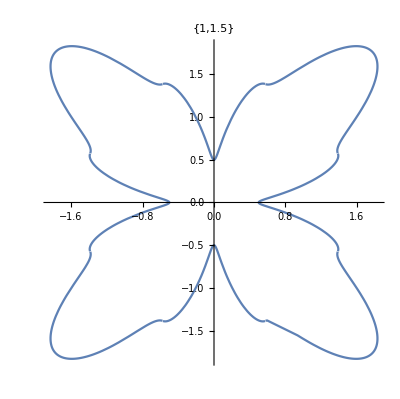
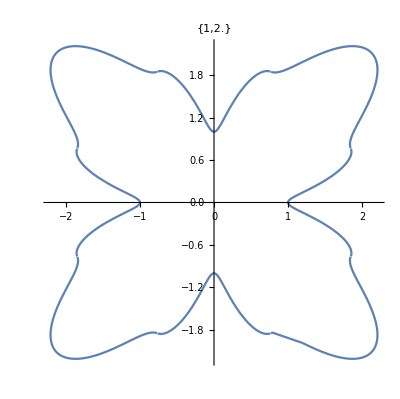
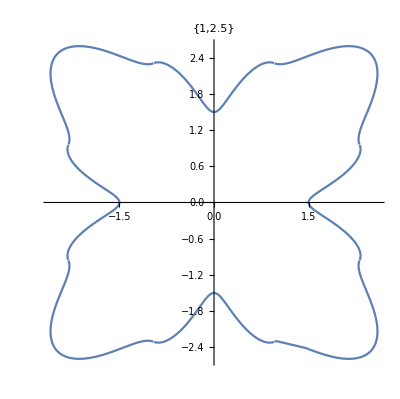
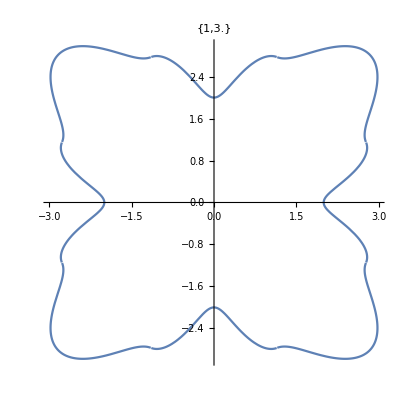
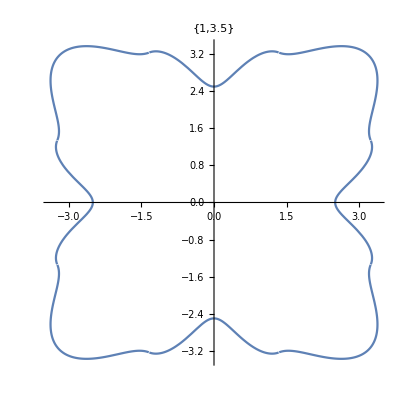
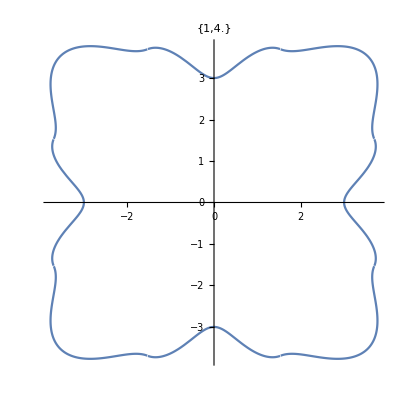
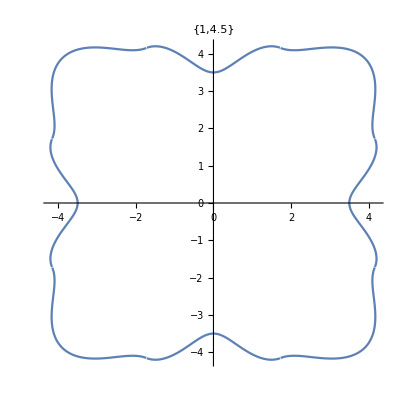

```mathematica
Table[PolarPlot[r[t, 2/a, b,4],{t,0,2Pi},PlotLabel->{a,b}],{a,6},{b,1,6,0.5}]
```

```mathematica
Table[{N[r[t,1/3,2.5,4]Cos[t]],N[r[t,1/3,2.5,4]Sin[t]]},{t,0,2 Pi,Pi/36}]
```

{{1.5,0.},{1.51473,0.132522},{1.56093,0.275233},{1.64816,0.441623},{1.82498,0.664237},{2.7714,1.29232},{2.85243,1.64685},{2.7974,1.95876},{2.66544,2.23657},{2.47487,2.47487},{2.23657,2.66544},{1.95876,2.7974},{1.64685,2.85243},{1.29232,2.7714},{0.664237,1.82498},{0.441623,1.64816},{0.275233,1.56093},{0.132522,1.51473},{0.,1.5},{-0.132522,1.51473},{-0.275233,1.56093},{-0.441623,1.64816},{-0.664237,1.82498},{-1.29232,2.7714},{-1.64685,2.85243},{-1.95876,2.7974},{-2.23657,2.66544},{-2.47487,2.47487},{-2.66544,2.23657},{-2.7974,1.95876},{-2.85243,1.64685},{-2.7714,1.29232},{-1.82498,0.664237},{-1.64816,0.441623},{-1.56093,0.275233},{-1.51473,0.132522},{-1.5,0.},{-1.51473,-0.132522},{-1.56093,-0.275233},{-1.64816,-0.441623},{-1.82498,-0.664237},{-2.7714,-1.29232},{-2.85243,-1.64685},{-2.7974,-1.95876},{-2.66544,-2.23657},{-2.47487,-2.47487},{-2.23657,-2.66544},{-1.95876,-2.7974},{-1.64685,-2.85243},{-1.29232,-2.7714},{-0.664237,-1.82498},{-0.441623,-1.64816},{-0.275233,-1.56093},{-0.132522,-1.51473},{0.,-1.5},{0.132522,-1.51473},{0.275233,-1.56093},{0.441623,-1.64816},{0.664237,-1.82498},{1.29232,-2.7714},{1.64685,-2.85243},{1.95876,-2.7974},{2.23657,-2.66544},{2.47487,-2.47487},{2.66544,-2.23657},{2.7974,-1.95876},{2.85243,-1.64685},{2.7714,-1.29232},{1.82498,-0.664237},{1.64816,-0.441623},{1.56093,-0.275233},{1.51473,-0.132522},{1.5,0.}}

```mathematica
Table[{N[r[t,2/3,3.5, 4]Cos[t]],N[r[t,2/3,3.5,4]Sin[t]]},{t,0,2 Pi,Pi/36}]
```

{{2.5,0.},{2.53095,0.22143},{2.62233,0.462388},{2.77225,0.742821},{2.99644,1.09062},{3.45417,1.61071},{3.57665,2.06498},{3.55284,2.48772},{3.41608,2.86643},{3.18198,3.18198},{2.86643,3.41608},{2.48772,3.55284},{2.06498,3.57665},{1.61071,3.45417},{1.09062,2.99644},{0.742821,2.77225},{0.462388,2.62233},{0.22143,2.53095},{0.,2.5},{-0.22143,2.53095},{-0.462388,2.62233},{-0.742821,2.77225},{-1.09062,2.99644},{-1.61071,3.45417},{-2.06498,3.57665},{-2.48772,3.55284},{-2.86643,3.41608},{-3.18198,3.18198},{-3.41608,2.86643},{-3.55284,2.48772},{-3.57665,2.06498},{-3.45417,1.61071},{-2.99644,1.09062},{-2.77225,0.742821},{-2.62233,0.462388},{-2.53095,0.22143},{-2.5,0.},{-2.53095,-0.22143},{-2.62233,-0.462388},{-2.77225,-0.742821},{-2.99644,-1.09062},{-3.45417,-1.61071},{-3.57665,-2.06498},{-3.55284,-2.48772},{-3.41608,-2.86643},{-3.18198,-3.18198},{-2.86643,-3.41608},{-2.48772,-3.55284},{-2.06498,-3.57665},{-1.61071,-3.45417},{-1.09062,-2.99644},{-0.742821,-2.77225},{-0.462388,-2.62233},{-0.22143,-2.53095},{0.,-2.5},{0.22143,-2.53095},{0.462388,-2.62233},{0.742821,-2.77225},{1.09062,-2.99644},{1.61071,-3.45417},{2.06498,-3.57665},{2.48772,-3.55284},{2.86643,-3.41608},{3.18198,-3.18198},{3.41608,-2.86643},{3.55284,-2.48772},{3.57665,-2.06498},{3.45417,-1.61071},{2.99644,-1.09062},{2.77225,-0.742821},{2.62233,-0.462388},{2.53095,-0.22143},{2.5,0.}}

```mathematica
Table[{N[r[t,1/2,2.5,4]Cos[t]],N[r[t,1/2,2.5, 4]Sin[t]]},{t,0,2 Pi,Pi/36}]
```

{{1.5,0.},{1.5248,0.133403},{1.60008,0.282137},{1.7318,0.464035},{1.95765,0.712527},{2.64344,1.23266},{2.77744,1.60355},{2.76483,1.93596},{2.6577,2.23007},{2.47487,2.47487},{2.23007,2.6577},{1.93596,2.76483},{1.60355,2.77744},{1.23266,2.64344},{0.712527,1.95765},{0.464035,1.7318},{0.282137,1.60008},{0.133403,1.5248},{0.,1.5},{-0.133403,1.5248},{-0.282137,1.60008},{-0.464035,1.7318},{-0.712527,1.95765},{-1.23266,2.64344},{-1.60355,2.77744},{-1.93596,2.76483},{-2.23007,2.6577},{-2.47487,2.47487},{-2.6577,2.23007},{-2.76483,1.93596},{-2.77744,1.60355},{-2.64344,1.23266},{-1.95765,0.712527},{-1.7318,0.464035},{-1.60008,0.282137},{-1.5248,0.133403},{-1.5,0.},{-1.5248,-0.133403},{-1.60008,-0.282137},{-1.7318,-0.464035},{-1.95765,-0.712527},{-2.64344,-1.23266},{-2.77744,-1.60355},{-2.76483,-1.93596},{-2.6577,-2.23007},{-2.47487,-2.47487},{-2.23007,-2.6577},{-1.93596,-2.76483},{-1.60355,-2.77744},{-1.23266,-2.64344},{-0.712527,-1.95765},{-0.464035,-1.7318},{-0.282137,-1.60008},{-0.133403,-1.5248},{0.,-1.5},{0.133403,-1.5248},{0.282137,-1.60008},{0.464035,-1.7318},{0.712527,-1.95765},{1.23266,-2.64344},{1.60355,-2.77744},{1.93596,-2.76483},{2.23007,-2.6577},{2.47487,-2.47487},{2.6577,-2.23007},{2.76483,-1.93596},{2.77744,-1.60355},{2.64344,-1.23266},{1.95765,-0.712527},{1.7318,-0.464035},{1.60008,-0.282137},{1.5248,-0.133403},{1.5,0.}}

```mathematica
rho[a_,b_]:=a+b Sin[8t];
Table[{N[rho[1,1/2]Cos[t]],N[rho[1,1/2]Sin[t]]},{t,0,2 Pi,Pi/36}]
```

{{1.,0.},{1.31637,0.115167},{1.46973,0.259153},{1.38418,0.370891},{1.10039,0.400509},{0.75132,0.350346},{0.491025,0.283494},{0.415798,0.291145},{0.519843,0.4362},{0.707107,0.707107},{0.849376,1.01225},{0.856008,1.22251},{0.716506,1.24103},{0.49489,1.0613},{0.283531,0.778996},{0.146747,0.547668},{0.0881431,0.499885},{0.0591444,0.676024},{0.,1.},{-0.115167,1.31637},{-0.259153,1.46973},{-0.370891,1.38418},{-0.400509,1.10039},{-0.350346,0.75132},{-0.283494,0.491025},{-0.291145,0.415798},{-0.4362,0.519843},{-0.707107,0.707107},{-1.01225,0.849376},{-1.22251,0.856008},{-1.24103,0.716506},{-1.0613,0.49489},{-0.778996,0.283531},{-0.547668,0.146747},{-0.499885,0.0881431},{-0.676024,0.0591444},{-1.,0.},{-1.31637,-0.115167},{-1.46973,-0.259153},{-1.38418,-0.370891},{-1.10039,-0.400509},{-0.75132,-0.350346},{-0.491025,-0.283494},{-0.415798,-0.291145},{-0.519843,-0.4362},{-0.707107,-0.707107},{-0.849376,-1.01225},{-0.856008,-1.22251},{-0.716506,-1.24103},{-0.49489,-1.0613},{-0.283531,-0.778996},{-0.146747,-0.547668},{-0.0881431,-0.499885},{-0.0591444,-0.676024},{0.,-1.},{0.115167,-1.31637},{0.259153,-1.46973},{0.370891,-1.38418},{0.400509,-1.10039},{0.350346,-0.75132},{0.283494,-0.491025},{0.291145,-0.415798},{0.4362,-0.519843},{0.707107,-0.707107},{1.01225,-0.849376},{1.22251,-0.856008},{1.24103,-0.716506},{1.0613,-0.49489},{0.778996,-0.283531},{0.547668,-0.146747},{0.499885,-0.0881431},{0.676024,-0.0591444},{1.,0.}}